El objetivo de esta tares es replicar las imágenes 4(c) y (d) del artículo Alonso-Lobo. Para ellos se programará una caminata cuántica en 2D como la descrita en el artículo. Las gráficas del artículo no se ajustan bien a Poisson, por lo que partiremos de que el unfolding no está bien.

Primero,definiremos los parámetros iniciales, tanto del rectángulo como de la moneda, tomando los descritos en el artículo (alpha y beta aquí es mejor que sean valores numéricos y no simbólicos)

```mathematica
L = 50; A = 25; (*rectángulo*)
alpha = Pi/4.; beta = Pi/3.; (*ángulos del operador moneda*)
esp = 60; showPlotRange = 5; (*espaciamientos*)
```

Ahora vamos a hacer un ordenamiento, transformar las coordenadas en indices lineales y luego se nos devolverá ese índice en el espacio de Hilbert

```mathematica
posIndex[l_,a_]:=(a-1)*L+l;
globalIndex[l_,a_,spin_]:=2*(posIndex[l,a]-1)+If[spin=="U",1,2];
```

Ahora, definiremos la matriz 2 x2 de la moneda

```mathematica
Ccoin[θ_]:={{Cos[θ],Sin[θ]},{-Exp[I*Pi/4] Sin[θ],Exp[I*Pi/4] Cos[θ]}};
C1=Ccoin[alpha];
C2=Ccoin[beta];
```

Ahora solo determinaremos el número de posiciones y la identidad sobre el subespacio de posiciones

```mathematica
Npos=L*A;dim=2*Npos; (*No de posiciones y dim del espacio de Hilbert*)
Ipos=IdentityMatrix[Npos,SparseArray]; (*Identidad*)
```

Ahora haremos una vectorización (o creación de una lista de coordenadas)

```mathematica
lVals=Flatten@Table[l,{a,1,A},{l,1,L}];
aVals=Flatten@Table[a,{a,1,A},{l,1,L}];
```

Definimos los índices globales

```mathematica
Uidx=globalIndex@@@Transpose[{lVals,aVals,ConstantArray["U",Length[lVals]]}];
Didx=globalIndex@@@Transpose[{lVals,aVals,ConstantArray["D",Length[lVals]]}];
```

Como ahora estamos trabajando una caminata en 2D, necesitamos hacer la construcción de los diferentes desplazamientos, para el horizontal tenemos:

```mathematica
targetU=MapThread[If[#1<L,globalIndex[#1+1,#2,"U"],globalIndex[L,#2,"D"]]&,{lVals,aVals}]; (*devulve el indice de la posicion (l + 1, a) con espin U, es decir mueve a la derecha manteniendo el espin*)
targetD=MapThread[If[#1>1,globalIndex[#1-1,#2,"D"],globalIndex[1,#2,"U"]]&,{lVals,aVals}];
rWm=Join[MapThread[{#1,#2}->1&,{targetU,Uidx}],MapThread[{#1,#2}->1&,{targetD,Didx}]]; (*resolver errores dimensionales*)

Wm=SparseArray[rWm,{dim,dim}];
```

y para el desplazamiento vertical tendremos:

```mathematica
targetU2=MapThread[If[#2<A,globalIndex[#1,#2+1,"U"],globalIndex[#1,A,"D"]]&,{lVals,aVals}];
targetD2=MapThread[If[#2>1,globalIndex[#1,#2-1,"D"],globalIndex[#1,1,"U"]]&,{lVals,aVals}];

rWn=Join[MapThread[{#1,#2}->1&,{targetU2,Uidx}],MapThread[{#1,#2}->1&,{targetD2,Didx}]];

Wn=SparseArray[rWn,{dim,dim}];
```

Ahora aplicaremos los operadores moneda a las posiciones

```mathematica
C1t=KroneckerProduct[C1,Ipos];
C2t=KroneckerProduct[C2,Ipos];
```

Ya podemos construir el operador de evolución completo

```mathematica
Qw=Wn.C2t.Wm.C1t;  (*libro*)
```

Agrego esta linea (ahora se tarda mucho menos porque Qw es un arreglo con valores numéricos):

```mathematica
eigvals=Eigenvalues[Normal[Qw]];
```

Ahora nos introduciremos en el problema del unfolding

```mathematica
phases=Mod[Arg[eigvals],2 Pi]; (*fase de c/eigenvalor -> radianes*)
fS=Sort[phases]; (*orden ascendente*)
Es=Differences[fS]; (*lista de N-1, espaciamientos vecinos*)
pEs=Mean[Es]; (*promedio*)
sUnfold=Es/pEs;  (*unfolding del paper*)
```

Con el unfolding, se busca que la densidad de estados (DOS) se vuelva plana. Así se ve antes del unfolding

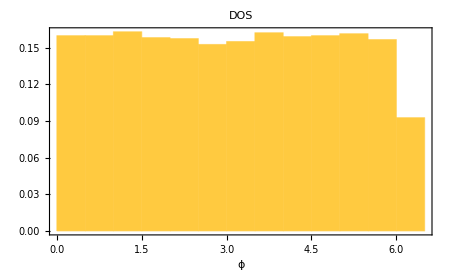

```mathematica
Histogram[fS,Automatic,"PDF",Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{"ϕ",""},PlotLabel->Style["DOS",Black,FontSize->22],ImageSize->450]
```

También con el unfolding se consigue que el espaciamiento promedio se vuelva 1:

```mathematica
sUnfold//Mean
```

1.

Ahora haremos la normalización

```mathematica
{edges,counts}=HistogramList[sUnfold,{0,showPlotRange,showPlotRange/esp}];
centers=MovingAverage[edges,2];
pdf=counts/Total[counts]/(showPlotRange/esp);
```

Definimos las curvas

```mathematica
poisson[s_]:=Exp[-s];
wigner[s_]:=(Pi/2) s Exp[-Pi s^2/4];
```

Ya podemos generar la imagen

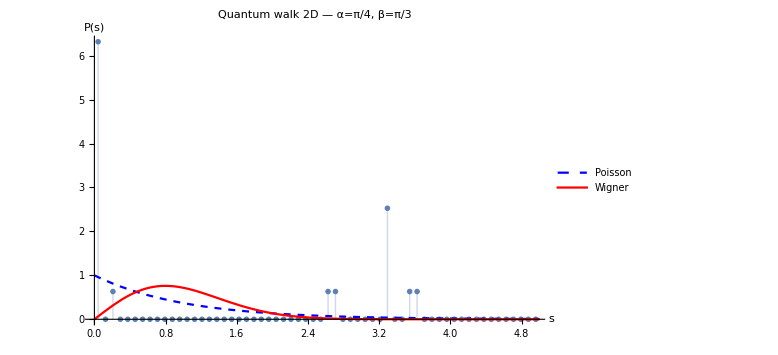

```mathematica
Show[ListPlot[Transpose[{centers,pdf}],
Filling->Axis,
Joined->False,
PlotMarkers->{"|",7},
AxesLabel->{"s","P(s)"},PlotLabel->Row[{"Quantum walk 2D — α=",NumberForm[alpha,{3,2}],", β=",NumberForm[beta,{3,2}]}]],Plot[{poisson[x],wigner[x]},{x,0,showPlotRange},PlotStyle->{Directive[Blue,Dashed],Directive[Red,Thick]},PlotLegends->{"Poisson","Wigner"}],ImageSize->Large]
```

Con Histogram podés directamente graficar el histograma:

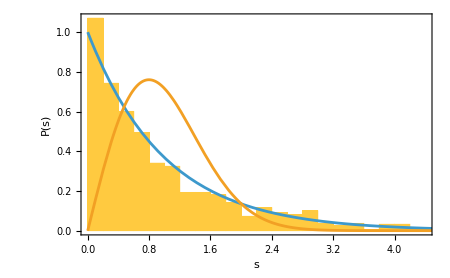

```mathematica
Show[
Histogram[sUnfold,Automatic,"PDF",Frame->True,FrameStyle->Directive[Black,FontSize->22],FrameLabel->{"s","P(s)"},ImageSize->450],
Plot[{poisson[s],wigner[s]},{s,0,5}]
]
```